```mathematica
SetDirectory[NotebookDirectory[]]
<< SSSDev`
```

C:\Users\caviness\Documents\Git\SSS-Code\Main

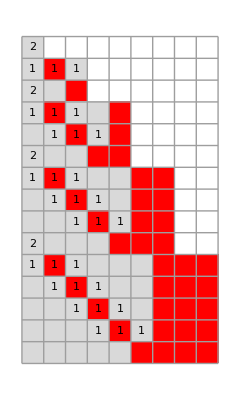


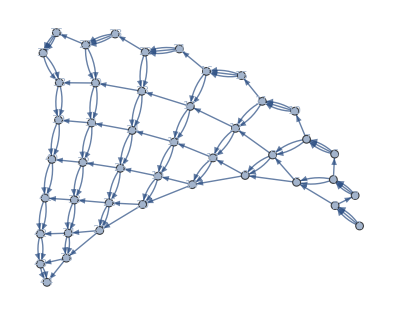
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
sss=SSS[{"ABA"->"AAB","A"->"ABA"}, "A",44,SSSMax->15, NetMethod -> GraphPlot];
```

```mathematica
sss["TRuleSet"]
```

{s[{0,lhsTag$3101_},{1,lhsTag$3102_},{0,lhsTag$3103_}]:>(AppendTo[$SSSRulesUsed,1];AppendTo[$SSSConnectionList,{lhsTag$3101,lhsTag$3102,lhsTag$3103}→$SSSTagIndex+{0,1,2}];s[{0,$SSSTagIndex++},{0,$SSSTagIndex++},{1,$SSSTagIndex++}]),s[{0,lhsTag$3105_}]:>(AppendTo[$SSSRulesUsed,2];AppendTo[$SSSConnectionList,{lhsTag$3105}→$SSSTagIndex+{0,1,2}];s[{0,$SSSTagIndex++},{1,$SSSTagIndex++},{0,$SSSTagIndex++}]),___:>AppendTo[$SSSRulesUsed,0]}

```mathematica
?*sss*
```

```mathematica
Context[]
```

Global`

```mathematica
Context[sss]
```

SSSDev`

```mathematica
Contexts[]
```

```mathematica
SSSDev`sss==sss
```

True

```mathematica
sss["Evolution"]
```

```mathematica
sss["RuleSet"]
```

{ABA→AAB,A→ABA}

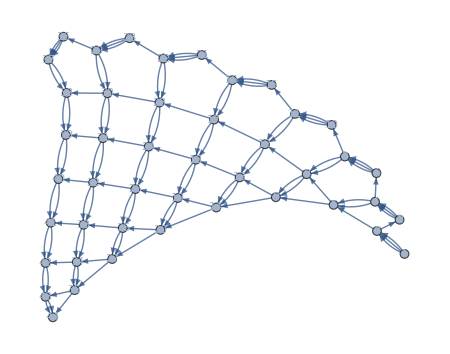
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
SSSDisplay[sss,SSSSize->100, NetSize->450]
```

```mathematica
FromReducedRankRuleSet@{"B"->"B"}
```

<|Index→146,QCode→424,RuleSet→{B→B}|>

```mathematica
FromReducedRankIndex[146]
```

<|Index→146,QCode→424,RuleSet→{B→B}|>

```mathematica
FromReducedRankQuinaryCode["424"]
```

<|Index→146,QCode→424,RuleSet→{B→B}|>

```mathematica
TestForIdentityRule@FromReducedRankRuleSet@{"B"->"B"}
```

<|Index→147,QCode→430,RuleSet→{BA→,→A}|>